```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"./models/DipoleDM/DipoleDM_FA/DipoleDM_FA",InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## chi1 → chi0+a

in total: 1 Particles insertion

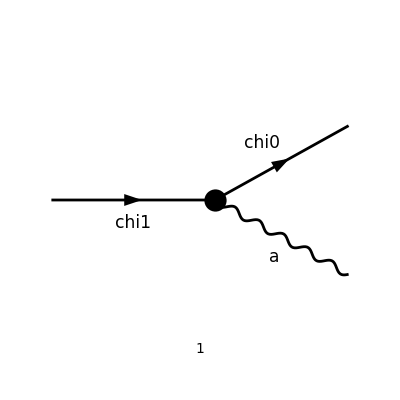

```mathematica
tops0 = CreateTopologies[0,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
chi1Dec=  { F[16]} -> {F[17],V[1]};
allDiags = InsertFields[tops0,chi1Dec, InsertionLevel-> {Particles},GenericModel->"./models/DipoleDM/DipoleDM_FA/DipoleDM_FA_fix"];
Paint[allDiags,ColumnsXRows->{2,1},ImageSize->{ 300,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True,SheetHeader->None];
```

```mathematica
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{p},OutgoingMomenta->{k1,k2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,TransversePolarizationVectors->{},Contract->True,ChangeDimension->4,FinalSubstitutions-> (M$FACouplings/.GS->gs)];
```

in total: 1 Particles amplitude

```mathematica
Simplify[amp]
```

(φ(OverBar[k1],M0)).(-ⅈ AAC ((γ̄·OverBar[k2]).(γ̄·(ε̄)^*(k2)).(γ̄)^6+(γ̄·OverBar[k2]).(γ̄·(ε̄)^*(k2)).(γ̄)^7-(γ̄·(ε̄)^*(k2)).(γ̄·OverBar[k2]).(γ̄)^6-(γ̄·(ε̄)^*(k2)).(γ̄·OverBar[k2]).(γ̄)^7)).(φ(p̄,M1))

## On - Shell Case :

```mathematica
FCClearScalarProducts[]
SP[p]=M1^2;
SP[k1]=M0^2;
SP[k2]=0;
SP[k1,k2]=Simplify[(SP[p]-SP[k1]-SP[k2])/2];
SP[p,k1]=Simplify[ExpandScalarProduct[SP[k1+k2,k1]]];
SP[p,k2]=Simplify[ExpandScalarProduct[SP[k1+k2,k2]]];
```

## Square amplitude

The factor of 1/2 is due to the average over the polarizations of χ_1.

```mathematica
ampSquared=(amp (ComplexConjugate[amp]))//SUNSimplify//FermionSpinSum[#,ExtraFactor->1/2]&//DiracSimplify//DoPolarizationSums[#,k2,0]&//Simplify
```

8 AAC^2 (M0^2-M1^2)^2

### Total Decay Rate

```mathematica
phaseSpacePrefactor[m1_,m2_,M_]:=1/(16 Pi M) Sqrt[1-(m1+m2)^2/M^2]*Sqrt[1-(m1-m2)^2/M^2];
totalDecayRate=phaseSpacePrefactor[M0,0,M1]*ampSquared//Simplify//ReplaceAll[#,Sqrt[x_] Sqrt[y_]:>Sqrt[ExpandAll[x y]]]&
```

(AAC^2 (M1^2-M0^2)^3)/(2 π M1^3)

```mathematica
totalDecayRate/.{AAC->10^(-3),M1->295.,M0->247.5} (* MG5 value -> 1.060802e-01 *)
```

0.10608